# Wolfram Weather

## Forecast

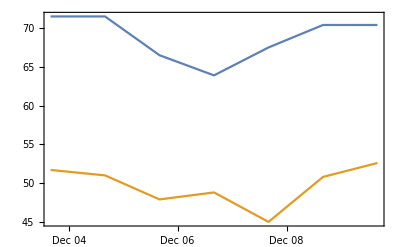

```mathematica
city=Entity["City", {"LosAngeles", "California", "UnitedStates"}];
location =EntityValue[city,"Coordinates"];
forecast=WeatherForecastData[location];
DateListPlot[{forecast["MaxTemperature"],forecast["MinTemperature"]}]
```

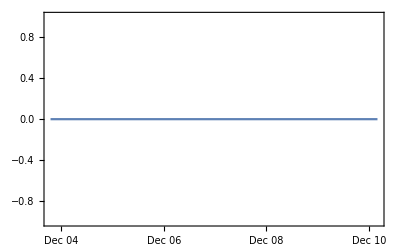

```mathematica
DateListPlot[forecast["PrecipitationAmount"]]
```

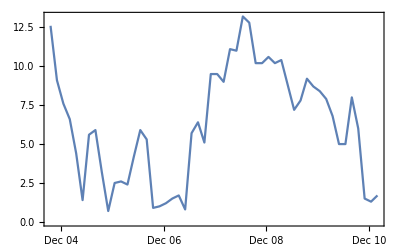

```mathematica
DateListPlot[forecast["WindSpeed"]]
```

## Celestial

### Seven-Day Moon Phases

```mathematica
sevenDays =NestList[DayPlus[#,1]&,Now,7];
Map[MoonPhase[#,"Icon"]&,sevenDays]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Sunset and Sunrise

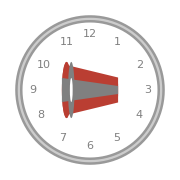
{-Graphics-,-Graphics-}

```mathematica
Map[ClockGauge,{Sunset[],Sunrise[]}]
```